```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
f={#1,Around[#2,#3]}&;
```

```mathematica
data1=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_100_dps.csv"];
data2=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_250_dps.csv"];
data3=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_500_dps.csv"];
data4=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_1000_dps.csv"];
data5=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_2000_dps.csv"];
data6=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_10000_dps.csv"];
data7=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_10_1000000_dps.csv"];data8=Import["Pythia/Tests/delta_phi_1e7_1014_1420_2641_2641_mpi.csv"];
```

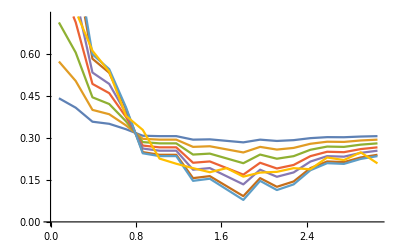

```mathematica
plot1=ListPlot[{data1,data2,data3,data4,data5,data6,data7,data8},PlotLegends->MaTeX/@{"\\sigma_{\\text{eff}}=10","\\sigma_{\\text{eff}}=25","\\sigma_{\\text{eff}}=50","\\sigma_{\\text{eff}}=100","\\sigma_{\\text{eff}}=200","\\sigma_{\\text{eff}}=1000","\\sigma_{\\text{eff}}=100000","\\text{MPI}"},Joined->True]
```

```mathematica
Export["dps1.pdf",plot1]
```

dps1.pdf

```mathematica
datapp=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp.csv"];
dataAu=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Au.csv"];
dataAl=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Al.csv"];
```

```mathematica
dataAu2=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Au_2.csv"];
dataAl2=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_Al_2.csv"];
```

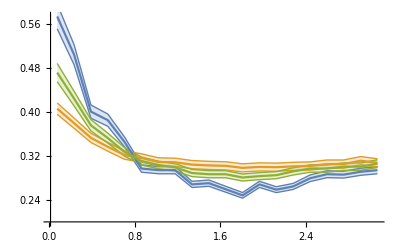

```mathematica
plot2=ListPlot[{f@@@datapp,f@@@dataAu,f@@@dataAl},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Au}","p+\\mathrm{Al}"},PlotRange->{All,{0.2,All}},Joined->True,IntervalMarkers->"Bands"]
```

```mathematica
Export["dps5.pdf",plot2]
```

dps5.pdf

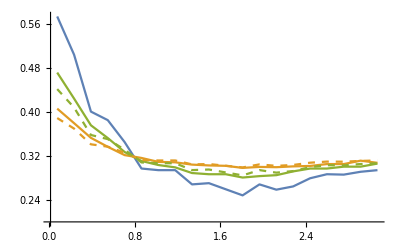

```mathematica
plot3=ListPlot[{f@@@datapp,f@@@dataAu,f@@@dataAl,f@@@dataAu2,f@@@dataAl2},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Au} \\ \\text{(nPDF)}","p+\\mathrm{Al} \\ \\text{(nPDF)}","p+\\mathrm{Au}","p+\\mathrm{Al}"},PlotRange->{All,{0.2,All}},Joined->True,IntervalMarkers->None,PlotStyle->{Automatic,Automatic,Automatic,{Dashed,ColorData[97,"ColorList"][[2]]},{Dashed,ColorData[97,"ColorList"][[3]]}}]
```

```mathematica
Export["dps6.pdf",plot3]
```

dps6.pdf

```mathematica
datapp1=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp_10.csv"];
datapp2=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp_15.csv"];
datapp3=Import["Pythia/STAR7/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp_100.csv"];
```

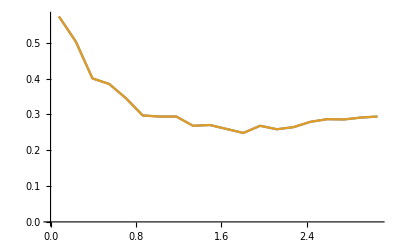

```mathematica
ListPlot[{f@@@datapp1,f@@@datapp2,f@@@datapp3},PlotLegends->MaTeX/@{"\\hat p_T=1.0","\\hat p_T=1.5"},Joined->True,IntervalMarkers->None]
```

```mathematica
dataBiasOff=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp_bias_off.csv"];
dataBiasOff2=Import["Pythia/Tests/Bias/delta_phi_1e8_1014_1420_2641_2641_250_dps_pp_bias_off.csv"];
dataBiasOn=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp_bias_on.csv"];
dataBiasOn2=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_250_dps_pp_bias_on_2.csv"];
```

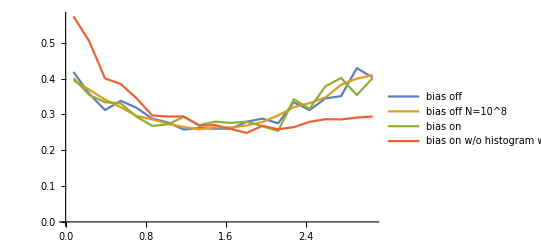

```mathematica
ListPlot[{f@@@dataBiasOff,f@@@dataBiasOff2,f@@@dataBiasOn,f@@@dataBiasOn2},PlotLegends->{"bias off","bias off N=10^8","bias on","bias on w/o histogram weight"},Joined->True,IntervalMarkers->None]
```

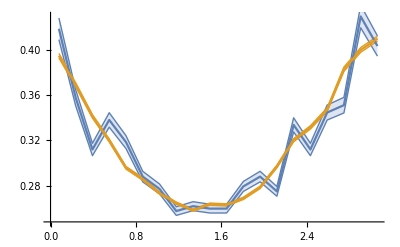

```mathematica
ListPlot[{f@@@dataBiasOff,f@@@dataBiasOff2},Joined->True,IntervalMarkers->"Bands"]
```

```mathematica
dataBias2=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_mpi_pp_bias_off.csv"];
dataBias3=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_mpi_pp_bias_on.csv"];
dataBias4=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_mpi_pp_bias_on_2.csv"];
dataBias5=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_mpi_pp_bias_on_3.csv"];
dataBias6=Import["Pythia/Tests/Bias/delta_phi_1e8_1014_1420_2641_2641_mpi_pp_bias_on.csv"];
```

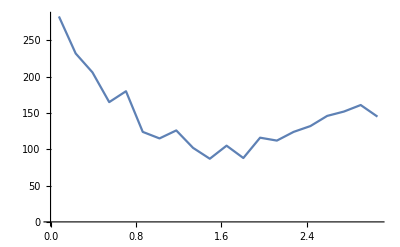

```mathematica
ListPlot[{f@@@dataBias2},Joined->True,IntervalMarkers->None]
```

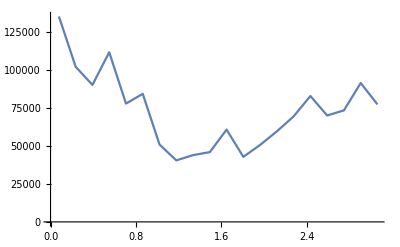

```mathematica
ListPlot[{f@@@dataBias3},Joined->True,IntervalMarkers->None]
```

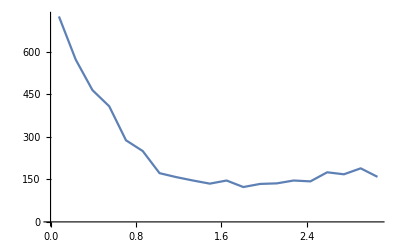

```mathematica
ListPlot[{f@@@dataBias4},Joined->True,IntervalMarkers->None]
```

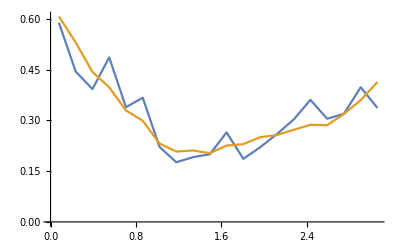

```mathematica
ListPlot[{f@@@dataBias5,f@@@dataBias6},Joined->True,IntervalMarkers->None]
```

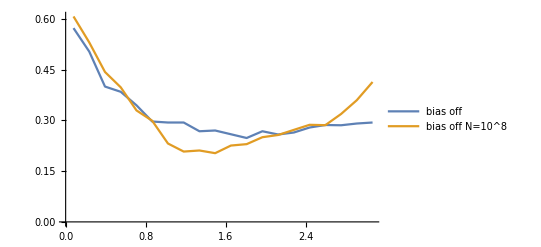

```mathematica
ListPlot[{f@@@dataBiasOn2,f@@@dataBias6},PlotLegends->{"bias off","bias off N=10^8","bias on","bias on w/o histogram weight"},Joined->True,IntervalMarkers->None]
```

```mathematica
sumTest1=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641_mpi.csv"];
sumTest2=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641_2641c_mpi.csv"];
sumTest3=Import["Pythia/Tests/Bias/delta_phi_1e7_1014_1420_2641__mpi.csv"];
```

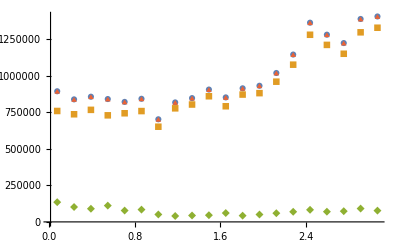

```mathematica
ListPlot[{f@@@sumTest3,f@@@sumTest2,f@@@sumTest1,Transpose[{sumTest2[[All,1]],sumTest2[[All,2]]+sumTest1[[All,2]]}]},PlotLegends->MaTeX/@{"y_2\\in \\left]-\\infty,\\infty\\right[","y_2\\notin [2.6, 4.1]","y_2\\in [2.6, 4.1]","\\Sigma"},PlotLabel->MaTeX["N=10^7, \\; p_T^1\\in [1.0, 1.4], \\; p_T^2\\in [1.4, 2.0], \\; y_1\\in [2.6, 4.1]"],PlotRange->All,PlotMarkers->{Automatic,Automatic,Automatic,{Automatic,0.02}},IntervalMarkers->None]
```

```mathematica
bias1=Import["Pythia/Tests/Bias/delta_phi_1e8_1014_1420_2641_2641_mpi_pp_bias_off.csv"];
bias2=Import["Pythia/Tests/Bias/delta_phi_1e8_1014_1420_2641_2641_mpi_pp_bias_on.csv"];
bias3=Import["Pythia/Tests/Bias/delta_phi_1e8_1014_1420_2641_2641_mpi_pp_bias_on_2.csv"];
```

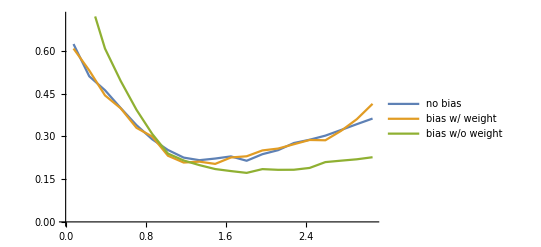

```mathematica
biasPlot=ListPlot[{f@@@bias1,f@@@bias2,f@@@bias3},Joined->True,PlotLegends->{"no bias","bias w/ weight","bias w/o weight"}]
```

```mathematica
Export["Pythia/Tests/Bias/bias.pdf",biasPlot]
```

Pythia/Tests/Bias/bias.pdf

```mathematica
sigmaeff1=Import["Pythia/Tests/sigma_eff/delta_phi_1e8_1014_1420_2641_2641_dps_100.csv"];
sigmaeff2=Import["Pythia/Tests/sigma_eff/delta_phi_1e8_1014_1420_2641_2641_dps_250.csv"];
sigmaeff3=Import["Pythia/Tests/sigma_eff/delta_phi_1e8_1014_1420_2641_2641_dps_500.csv"];
sigmaeff4=Import["Pythia/Tests/sigma_eff/delta_phi_1e8_1014_1420_2641_2641_dps_1000.csv"];
sigmaeff5=Import["Pythia/Tests/sigma_eff/delta_phi_1e8_1014_1420_2641_2641_dps_2000.csv"];
```

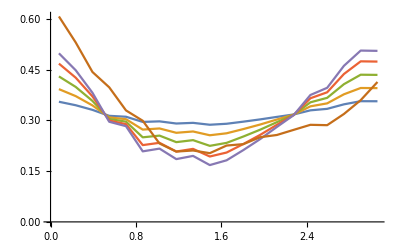

```mathematica
sigmaeffPlot=ListPlot[{f@@@sigmaeff1,f@@@sigmaeff2,f@@@sigmaeff3,f@@@sigmaeff4,f@@@sigmaeff5,f@@@bias2},Joined->True,PlotLegends->MaTeX/@{"\\sigma_{\\text{eff}}=10","\\sigma_{\\text{eff}}=25","\\sigma_{\\text{eff}}=50","\\sigma_{\\text{eff}}=100","\\sigma_{\\text{eff}}=200","\\text{MPI}"},IntervalMarkers->None]
```

```mathematica
pThat1=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_1014_1420_2641_2641_dps_250_15.csv"];
pThat2=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_1014_1420_2641_2641_dps_250_20.csv"];
pThat3=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_1014_1420_2641_2641_dps_250_soft.csv"];
```

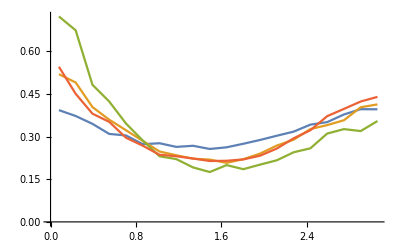

```mathematica
pThatPlot1=ListPlot[{f@@@sigmaeff2,f@@@pThat1,f@@@pThat2,f@@@pThat3},Joined->True,PlotLegends->MaTeX/@{"\\hat p_T=1.0","\\hat p_T=1.5","\\hat p_T=2.0","\\text{SoftQCD (non-diffractive)}"},IntervalMarkers->None]
```

```mathematica
pThat4=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_2024_2428_2641_2641_dps_250_10.csv"];
pThat5=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_2024_2428_2641_2641_dps_250_15.csv"];
pThat6=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_2024_2428_2641_2641_dps_250_20.csv"];
pThat7=Import["Pythia/Tests/pT_hat_min/delta_phi_1e8_2024_2428_2641_2641_dps_250_soft.csv"];
```

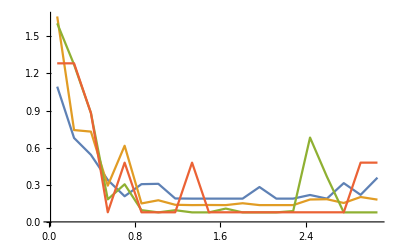

```mathematica
pThatPlot2=ListPlot[{f@@@pThat4,f@@@pThat5,f@@@pThat6,f@@@pThat7},Joined->True,PlotLegends->MaTeX/@{"\\hat p_T=1.0","\\hat p_T=1.5","\\hat p_T=2.0","\\text{SoftQCD (non-diffractive)}"},IntervalMarkers->None,PlotRange->All]
```

```mathematica
nuclearpp25=Import["Pythia/Tests/Nuclear/HardQCD/pp_25.csv"];
nuclearAl25=Import["Pythia/Tests/Nuclear/HardQCD/Al_25.csv"];
nuclearAu25=Import["Pythia/Tests/Nuclear/HardQCD/Au_25.csv"];
```

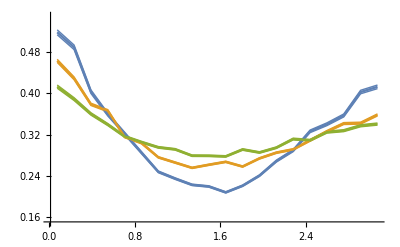

```mathematica
nuclearPlot1=ListPlot[{f@@@nuclearpp25,f@@@nuclearAl25,f@@@nuclearAu25},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Al}","p+\\mathrm{Au}"},PlotRange->{All,{0.15,0.55}},Joined->True,IntervalMarkers->"Bands",PlotLabel->MaTeX["\\sigma_{\\text{eff}}=25, \\ \\hat p_T=1.5"]]
```

```mathematica
Export["Pythia/Tests/Nuclear/HardQCD/nuclear1.pdf",nuclearPlot1]
```

Pythia/Tests/Nuclear/HardQCD/nuclear1.pdf

```mathematica
nuclearpp10=Import["Pythia/Tests/Nuclear/HardQCD/pp_10.csv"];
nuclearAl10=Import["Pythia/Tests/Nuclear/HardQCD/Al_10.csv"];
nuclearAu10=Import["Pythia/Tests/Nuclear/HardQCD/Au_10.csv"];
```

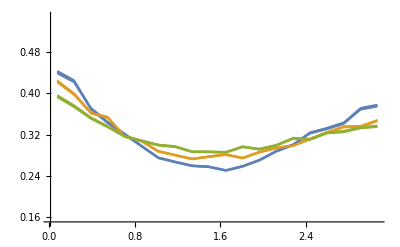

```mathematica
nuclearPlot2=ListPlot[{f@@@nuclearpp10,f@@@nuclearAl10,f@@@nuclearAu10},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Al}","p+\\mathrm{Au}"},PlotRange->{All,{0.15,0.55}},Joined->True,IntervalMarkers->"Bands",PlotLabel->MaTeX["\\sigma_{\\text{eff}}=10, \\ \\hat p_T=1.5"]]
```

```mathematica
Export["Pythia/Tests/Nuclear/HardQCD/nuclear2.pdf",nuclearPlot2]
```

Pythia/Tests/Nuclear/HardQCD/nuclear2.pdf

```mathematica
nuclearpp25soft=Import["Pythia/Tests/Nuclear/SoftQCD/pp_25.csv"];
nuclearAl25soft=Import["Pythia/Tests/Nuclear/SoftQCD/Al_25.csv"];
nuclearAu25soft=Import["Pythia/Tests/Nuclear/SoftQCD/Au_25.csv"];
```

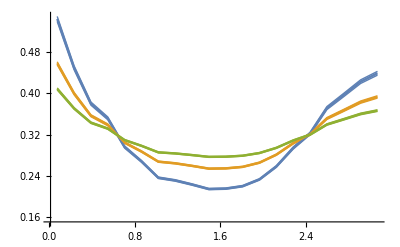

```mathematica
nuclearPlot3=ListPlot[{f@@@nuclearpp25soft,f@@@nuclearAl25soft,f@@@nuclearAu25soft},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Al}","p+\\mathrm{Au}"},PlotRange->{All,{0.15,0.55}},Joined->True,IntervalMarkers->"Bands",PlotLabel->MaTeX["\\sigma_{\\text{eff}}=25 \\text{ (SoftQCD)}"]]
```

```mathematica
Export["Pythia/Tests/Nuclear/SoftQCD/nuclear3.pdf",nuclearPlot3]
```

Pythia/Tests/Nuclear/SoftQCD/nuclear3.pdf

```mathematica
nuclearpp10soft=Import["Pythia/Tests/Nuclear/SoftQCD/pp_10.csv"];
nuclearAl10soft=Import["Pythia/Tests/Nuclear/SoftQCD/Al_10.csv"];
nuclearAu10soft=Import["Pythia/Tests/Nuclear/SoftQCD/Au_10.csv"];
```

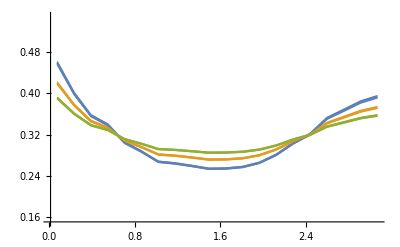

```mathematica
nuclearPlot4=ListPlot[{f@@@nuclearpp10soft,f@@@nuclearAl10soft,f@@@nuclearAu10soft},PlotLegends->MaTeX/@{"p+p","p+\\mathrm{Al}","p+\\mathrm{Au}"},PlotRange->{All,{0.15,0.55}},Joined->True,IntervalMarkers->"Bands",PlotLabel->MaTeX["\\sigma_{\\text{eff}}=10 \\text{ (SoftQCD)}"]]
```

```mathematica
Export["Pythia/Tests/Nuclear/SoftQCD/nuclear4.pdf",nuclearPlot4]
```

Pythia/Tests/Nuclear/SoftQCD/nuclear4.pdf

```mathematica
error1=Import["Pythia/Tests/Error Analysis/pp_none.csv"];
error2=Import["Pythia/Tests/Error Analysis/pp_cs.csv"];
error3=Import["Pythia/Tests/Error Analysis/pp_cs_hf.csv"];
```

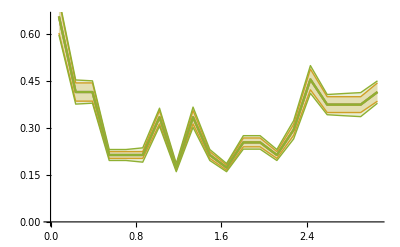

```mathematica
errorPlot1=ListPlot[{f@@@error1,f@@@error2,f@@@error3},Joined->True,IntervalMarkers->"Bands"]
```

```mathematica
pTWindowSoft=Import/@SortBy[FileNames["Pythia/Tests/pT/SoftQCD/*.csv"],ToExpression[StringDrop[FileBaseName[#],4]]&];
```

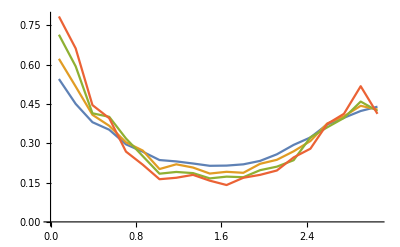

```mathematica
ListPlot[(f@@@#&/@pTWindowSoft)[[;;4]],Joined->True,IntervalMarkers->None,PlotLegends->MaTeX/@{"1.0<p_T^1<1.4, 1.4<p_T^2<2.0","1.1<p_T^1<1.5, 1.5<p_T^2<2.1","1.2<p_T^1<1.6, 1.6<p_T^2<2.2","1.3<p_T^1<1.7, 1.7<p_T^2<2.3"}]
```

```mathematica
pTWindowHard=Import/@SortBy[FileNames["Pythia/Tests/pT/HardQCD/*.csv"],ToExpression[StringDrop[FileBaseName[#],4]]&];
```

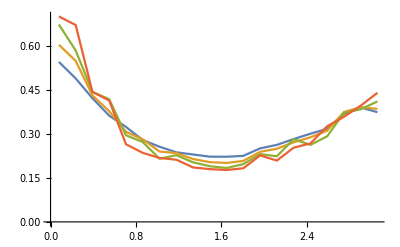

```mathematica
ListPlot[(f@@@#&/@pTWindowHard)[[;;4]],Joined->True,IntervalMarkers->None,PlotLegends->MaTeX/@{"1.0<p_T^1<1.4, 1.4<p_T^2<2.0","1.1<p_T^1<1.5, 1.5<p_T^2<2.1","1.2<p_T^1<1.6, 1.6<p_T^2<2.2","1.3<p_T^1<1.7, 1.7<p_T^2<2.3"}]
```